```mathematica
(*Define Constants*)G=6.67*10^-11;
ME=5.97*10^24;
R=6.3*10^6;
m=100;
v1=Sqrt[2*G*ME/R];
v0=v1 {Cos[Pi/4],Sin[Pi/4]};

dt=1;
tmax=8600;

(*Initialize Ball Position and Velocity*)
ballPos={R,0};
ballVel=v0;

(*Preallocate arrays for efficiency*)
numSteps=Ceiling[tmax/dt];
positions=Table[{0,0},{numSteps}];
kineticEnergy=Table[0,{numSteps}];
potentialEnergy=Table[0,{numSteps}];
totalEnergy=Table[0,{numSteps}];

doBreak=False;

(*Time Evolution*)
Do[r=Norm[ballPos];
If[r<R,doBreak=True];(*Stop if it hits the surface*)If[doBreak,Break[]];
F=-G ME m Normalize[ballPos]/r^2;
a=F/m;
ballVel+=a dt;
ballPos+=ballVel dt;
positions[[t]]=ballPos;
kineticEnergy[[t]]=0.5 m Norm[ballVel]^2;
potentialEnergy[[t]]=-G ME m/r;
totalEnergy[[t]]=kineticEnergy[[t]]+potentialEnergy[[t]];,{t,numSteps}]

(*Remove unused entries*)
positions=DeleteCases[positions,{0,0}];
kineticEnergy=DeleteCases[kineticEnergy,0];
potentialEnergy=DeleteCases[potentialEnergy,0];
totalEnergy=DeleteCases[totalEnergy,0];
rVals=Norm/@positions;

(*Plot Energies*)
energyPlot=ListLinePlot[{Transpose[{rVals,kineticEnergy}],Transpose[{rVals,potentialEnergy}],Transpose[{rVals,totalEnergy}]},PlotStyle->{Red,Blue,Purple},PlotLegends->{"Kinetic Energy","Potential Energy","Total Energy"},AxesLabel->{"r [m]","E [J]"},GridLines->Automatic];

(*Animation of Motion*)
trajectory=Table[Graphics[{Sphere[{0,0},R],Yellow,Sphere[positions[[i]],R/20]}],{i,1,Length[positions],10}];

animation=ListAnimate[trajectory];

(*Calculate r2*)
r2=G ME/(-0.5 v1^2+G ME/R);
Print["r2 = ",r2," m"];

grid=Grid[{{animation,energyPlot}}];
grid
```

r2 = -5.34454×10^22 m

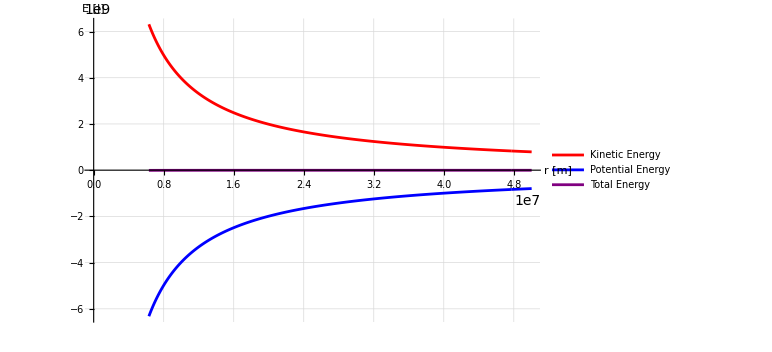

```mathematica
energyPlot=ListLinePlot[{Transpose[{rVals,kineticEnergy}],Transpose[{rVals,potentialEnergy}],Transpose[{rVals,totalEnergy}]},PlotStyle->{Red,Blue,Purple},PlotLegends->{"Kinetic Energy","Potential Energy","Total Energy"},AxesLabel->{"r [m]","E [J]"},GridLines->Automatic,ImageSize->Large (*Makes the plot larger*)];

(*Arrange Animation and Plot in a Grid*)
grid=Grid[{{animation},{energyPlot}},Alignment->Center,Spacings->{1,1}];

grid
```